# Caminatas cuánticas

## Importando cosas

```mathematica
Get[NotebookDirectory[]<>"../AmadoTemp/DTQW.wl"]
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
<<MaTeX`
```

## Definiendo variables

```mathematica
IndigoC=RGBColor["#729cfc"];
AquaC=RGBColor["#4bd7e5"];
DeepBlueC=RGBColor["#1e2c88"];
```

```mathematica
qlabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"Labels_pos.pdf","Labels_prob.pdf"};
clabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"Labels_pos.pdf","Labels_probc.pdf"};
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
PlotRange->All,
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

```mathematica
TeXLabel[tlist_List]:=MaTeX[
"\\begin{gathered}\n"<>Fold[
StringJoin[#1,"\\\\\n",#2]&,ToString@StringForm["\\text{``}",#]&/@tlist
]<>"\n\\end{gathered}",
FontSize->14,
Magnification->1.3,
"Preamble"->{"\\usepackage{physics}"}
]
```

## Inicializaciones

```mathematica
InitializeDTQW[2,201]
MakeCoin[1/2,0,0];
MakeShift[];
MakeUnitary[];
```

```mathematica
plotlist={};
```

## Results

### Caminata clásica

```mathematica
probsC=Module[{n=100},
Riffle[Binomial[n,#]/2^n&/@Range[0,n],0]
];
```

```mathematica
Total@probsC
```

1

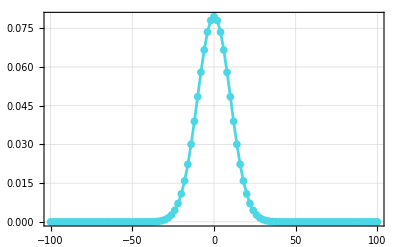

```mathematica
plotC=ListLinePlot[{Range[-100,100,2],probsC[[;;;;2]]}ᵀ,
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100"}],
FrameLabel->clabels,
PlotStyle->AquaC
]
AppendTo[plotlist,ToString@Unevaluated@plotC];
```

### Caminatas cuánticas (sin decoherencia)

#### Estado inicial (+_y)_c⊗0_p

Empezar hablando de lo que son las caminatas cuánticas y mostrar un ejemplo de una caminata

```mathematica
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{ⅈ/(√2),1,0}}]

```mathematica
rhof0=#.#†&@DTQW2[psi0,100];
```

```mathematica
probs0=Abs@Diagonal@MatrixPartialTrace[rhof0,1,{2,201}];
```

```mathematica
Total@probs0
```

1.

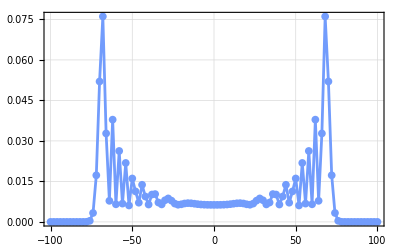

```mathematica
plot0=ListLinePlot[{Range[-100,100,2],probs0[[;;;;2]]}ᵀ,
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100 – Estado inicial: $\\ket{+_y}\\otimes\\ket{0}$"}],
FrameLabel->qlabels,
PlotStyle->IndigoC
]
AppendTo[plotlist,ToString@Unevaluated@plot0];
```

#### Estados iniciales 0⊗0 y 1⊗0

Las caminatas varían según condiciones iniciales de la moneda (idea de las condiciones)

```mathematica
psi1=VectorState[{{1,0,0}}];
psi2=VectorState[{{1,1,0}}];
```

```mathematica
rhof1=#.#†&@DTQW2[psi1,100];
rhof2=#.#†&@DTQW2[psi2,100];
```

```mathematica
probs1=Abs@Diagonal@MatrixPartialTrace[rhof1,1,{2,201}];
probs2=Abs@Diagonal@MatrixPartialTrace[rhof2,1,{2,201}];
```

```mathematica
Total/@{probs1,probs2}
```

{1.,1.}

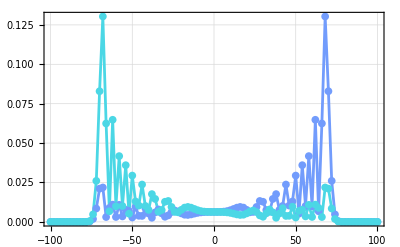

```mathematica
plot1y2=ListLinePlot[{
{Range[-100,100,2],probs1[[;;;;2]]}ᵀ,
{Range[-100,100,2],probs2[[;;;;2]]}ᵀ
},
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100"}],
FrameLabel->qlabels,
PlotStyle->{IndigoC,AquaC},
PlotLegends->(MaTeX[#,
"Preamble"->{"\\usepackage{physics}"},
FontSize->12,
Magnification->1.3
]&/@{"\\ket{0}\\otimes\\ket{0}","\\ket{1}\\otimes\\ket{0}"})
]
AppendTo[plotlist,ToString@Unevaluated@plot1y2];
```

#### Ejemplos más variados

```mathematica
psi3=VectorState[{{1/Sqrt[2],0,0},{1/Sqrt[2],1,0}}];
psi4=VectorState[{{1/Sqrt[2],0,20},{ⅈ/Sqrt[2],1,-20}}];
```

```mathematica
rhof3=#.#†&@DTQW2[psi3,100];
rhof4=#.#†&@DTQW2[psi4,100];
```

```mathematica
probs3=Abs@Diagonal@MatrixPartialTrace[rhof3,1,{2,201}];
probs4=Abs@Diagonal@MatrixPartialTrace[rhof4,1,{2,201}];
```

```mathematica
Total/@{probs3,probs4}
```

{1.,1.}

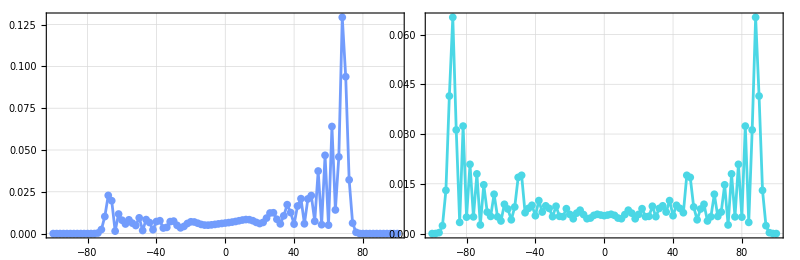

```mathematica
GraphicsGrid[{{
plot3=ListLinePlot[{Range[-100,100,2],probs3[[;;;;2]]}ᵀ,
plotargs,
FrameLabel->qlabels,
PlotStyle->IndigoC
],
plot4=ListLinePlot[{Range[-100,100,2],probs4[[;;;;2]]}ᵀ,
DeleteCases[plotargs,FrameLabel->_],
FrameLabel->{
Import[NotebookDirectory[]<>"Labels_pos.pdf",{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]],
None
},
FrameTicksStyle->{Directive[Opacity->0,FontSize->0],None},
PlotStyle->AquaC
]
}},
Spacings->{Scaled[-0.15],0}
]
AppendTo[plotlist,ToString@Unevaluated@plot3];
AppendTo[plotlist,ToString@Unevaluated@plot4];
```

### Caminatas con decoherencia

#### Introduciendo decoherencia

```mathematica
psi5=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
```

```mathematica
rhof5=DTQW2wDecoherence[psi5,0.99,100];
```

```mathematica
probs5=Abs@Diagonal@MatrixPartialTrace[rhof5,1,{2,201}];
```

```mathematica
Total[probs5]
```

1.

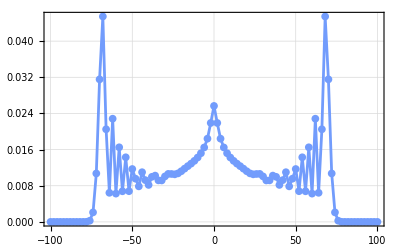

```mathematica
plot5=ListLinePlot[{Range[-100,100,2],probs5[[;;;;2]]}ᵀ,
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100 – Estado inicial: $\\ket{+_y}\\otimes\\ket{0}$","Decoherencia: 0.01"}],
FrameLabel->qlabels,
PlotStyle->IndigoC
]
AppendTo[plotlist,ToString@Unevaluated@plot5];
```

#### Comparativa clásica vs cuántica vs cuántica w/decoherencia

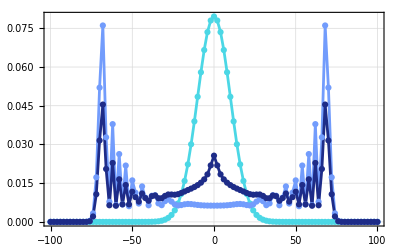

```mathematica
plotMix=ListLinePlot[{
{Range[-100,100,2],probsC[[;;;;2]]}ᵀ,
{Range[-100,100,2],probs0[[;;;;2]]}ᵀ,
{Range[-100,100,2],probs5[[;;;;2]]}ᵀ
},
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100 – Estado inicial: $\\ket{+_y}\\otimes\\ket{0}$"}],
FrameLabel->qlabels,
PlotStyle->{AquaC,IndigoC,DeepBlueC},
PlotLegends->(MaTeX[#,
"Preamble"->{"\\usepackage{physics}"},
FontSize->12,
Magnification->1.3
]&/@{"\\text{RW}","\\text{DTQW}","\\text{DTQW w/d 0.01}"})
]
AppendTo[plotlist,ToString@Unevaluated@plotMix];
```

#### Gradiente variando p

```mathematica
psi6=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
```

```mathematica
rhof6G=DTQW2wDecoherence[psi6,#,100]&/@(0.+Range[10]/1000);
```

```mathematica
probs6G=Abs@Diagonal@MatrixPartialTrace[#,1,{2,201}]&/@rhof6G;
```

```mathematica
Total/@probs6G
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

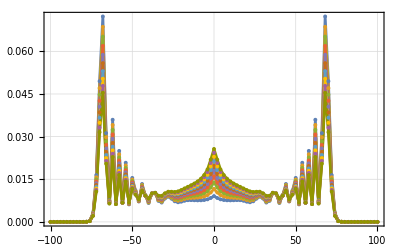

```mathematica
plot6=ListLinePlot[Evaluate@Table[{Range[-100,100,2],probs[[;;;;2]]}ᵀ,{probs,probs6G}],
plotargs,
PlotLabel->TeXLabel[{"Estado inicial: $\\ket{+_y}\\otimes\\ket{0}$"}],
FrameLabel->qlabels,
PlotLegends->(MaTeX[#,
"Preamble"->{"\\usepackage{physics}"},
ContentPadding->False,
FontSize->12,
Magnification->1.3
]&/@N[Range[10]/1000]),
ImageSize->Scaled[0.38]
]
AppendTo[plotlist,ToString@Unevaluated@plot6];
```

#### Recuperando la caminata clásica

```mathematica
psi7=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
```

```mathematica
rhof7=DTQW2wDecoherence[psi7,0.5,100];
```

```mathematica
probs7=Abs@Diagonal@MatrixPartialTrace[rhof7,1,{2,201}];
```

```mathematica
Total[probs7]
```

1.

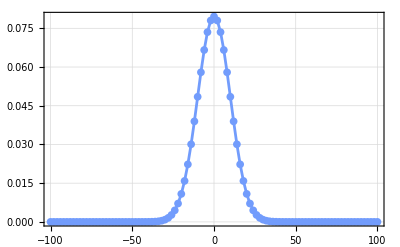

```mathematica
plot7=ListLinePlot[{Range[-100,100,2],probs7[[;;;;2]]}ᵀ,
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100 – Estado inicial: $\\ket{+_y}\\otimes\\ket{0}$","Decoherencia: 0.5"}],
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

```mathematica
AppendTo[plotlist,ToString@Unevaluated@plot7];
```

#### Análogo clásico de estados iniciales de superposición

Propuesta de una caminata clásica con dos caminantes usando decoherencia

```mathematica
psi8=VectorState[{{1/Sqrt[2],0,20},{ⅈ/Sqrt[2],1,-20}}];
```

```mathematica
rhof8=DTQW2wDecoherence[psi8,0.5,100];
```

```mathematica
probs8=Abs@Diagonal@MatrixPartialTrace[rhof8,1,{2,201}];
```

```mathematica
Total@probs8
```

1.

Dos caminantes en una misma línea

```mathematica
probsC2=Module[{n=100},
p1=(ConstantArray[0,20]~Join~ Riffle[Binomial[n,#]&/@Range[0,n],0]/2^(n+1))[[;;201]];
p2=( Riffle[Binomial[n,#]&/@Range[0,n],0]~Join~ConstantArray[0,20]/2^(n+1))[[21;;]];
p1+p2
];
```

```mathematica
probsC2//Length
```

201

```mathematica
Total@probsC2//N
```

1.

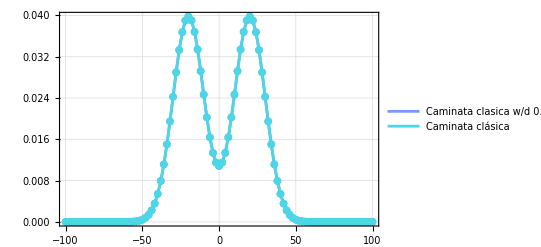

```mathematica
plot8yC2=ListLinePlot[{
{Range[-100,100,2],probs8[[;;;;2]]}ᵀ,
{Range[-100,100,2],probsC2[[;;;;2]]}ᵀ
},
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100"}],
FrameLabel->qlabels,
PlotStyle->{IndigoC,AquaC},
PlotLegends->{"Caminata clasica w/d 0.5","Caminata clásica"}
]
AppendTo[plotlist,ToString@Unevaluated@plot8yC2];
```

#### La transición cuántico–clásica no depende de la moneda

```mathematica
psi9=VectorState[{{1,0,0}}];
```

```mathematica
rhof9=DTQW2wDecoherence[psi9,0.02,100];
```

```mathematica
probs9=Abs@Diagonal@MatrixPartialTrace[rhof9,1,{2,201}];
```

```mathematica
Total[probs9]
```

1.

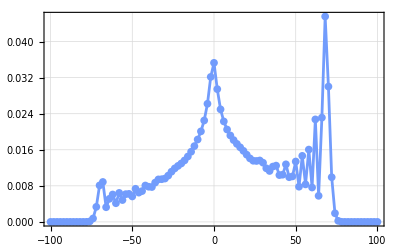

```mathematica
plot9=ListLinePlot[{Range[-100,100,2],probs9[[;;;;2]]}ᵀ,
plotargs,
PlotLabel->TeXLabel[{"Pasos: 100 – Estado inicial: $\\ket{0}\\otimes\\ket{0}$","Decoherencia: 0.98"}],
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

```mathematica
AppendTo[plotlist,ToString@Unevaluated@plot9];
```

### Caminatas de distintos operadores

Por hacer... (hay que arreglar el operador de shift)

## Exportando los resultados

```mathematica
Do[
Export[NotebookDirectory[]<>"../Results/"<>plot<>".pdf",ToExpression[plot],"PDF"],{plot,DeleteDuplicates[plotlist]}
]
```